# MGDrivE: Yorkeys Knob Analysis

## 0) Functions

```mathematica
<<colorBlender`
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Single Experiment Dynamics

Load Data

```mathematica
SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/ThresholdDependent"];
```

```mathematica
(*Experiment name = folder name*)
experimentName="TranslocationsFineScale";
timeRange={1,360};
releasesStart=20;
(**)
directoryData=Directory[]<>"/"<>experimentName<>"/";
experimentFolders=FileNames["E*",directoryData];
(**)
cellFolder=experimentFolders[[2]];
sweepID={null,geography,driveSystem,releasesNumber,coverage}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
releaseTimes={releasesStart,(releasesNumber*8)+releasesStart};
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM*","AF1*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(**)
genotypes=Import[filenamesMale[[20]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
```

{ⅇ,2,1,5,100}

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
aabb | aaBb | aaBB | Aabb | AaBb | AaBB | AAbb | AABb | AABB

Define Color Palette

```mathematica
originalColorsValues={
{100,60,0,0},
{60,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid;
maxPopSize=aggregatedGroupData//Flatten//Max;
SwatchLegend[rgbColors,genotypesGroups[[All,2]]
,LabelStyle->30
,LegendMarkerSize->25
]
(*Export[dataFolderName<>experimentName<>"_03.png",%,ImageResolution->500];*)
```

Aggregate Data By Genotype

```mathematica
(*Grouped Genotypes*)
genotypesGroups={
{{1,1,2,2,3,3,4,5,6,1,1,2,4,4,5,7,7,8},"W"},
{{4,5,6,7,7,8,8,9,9,2,3,3,5,6,6,8,9,9},"D"}
};
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
```

Plot

### Normalized

```mathematica
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
(**)
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]],releaseTimes[[2]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots;
Show[matrixPlots]
(*Export[dataFolderName<>experimentName<>"_01A.png",%,ImageSize->5000]*)
```

-Graphics-

### Normalized Split

```mathematica
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
(**)
aspectRatio=10;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]],releaseTimes[[2]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,.00001],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,.00001]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.25*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
Show[matrixPlots]
Transpose[{matrixPlots}]//Grid
(*Export[dataFolderName<>experimentName<>"_01C.png",%,ImageSize->5000]*)
```

-Graphics-

-Graphics-
-Graphics-

### Un-Normalized

```mathematica
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.0025]]
,FrameLabel->{
{Style["Time",35],None},
{None,Style[Rotate["House ID",π],35]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]],releaseTimes[[2]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},2*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
Show[matrixPlots]
(*Export[dataFolderName<>experimentName<>"_01B.png",%,ImageSize->5000]*)
```

-Graphics-

### BarChart

```mathematica
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
```

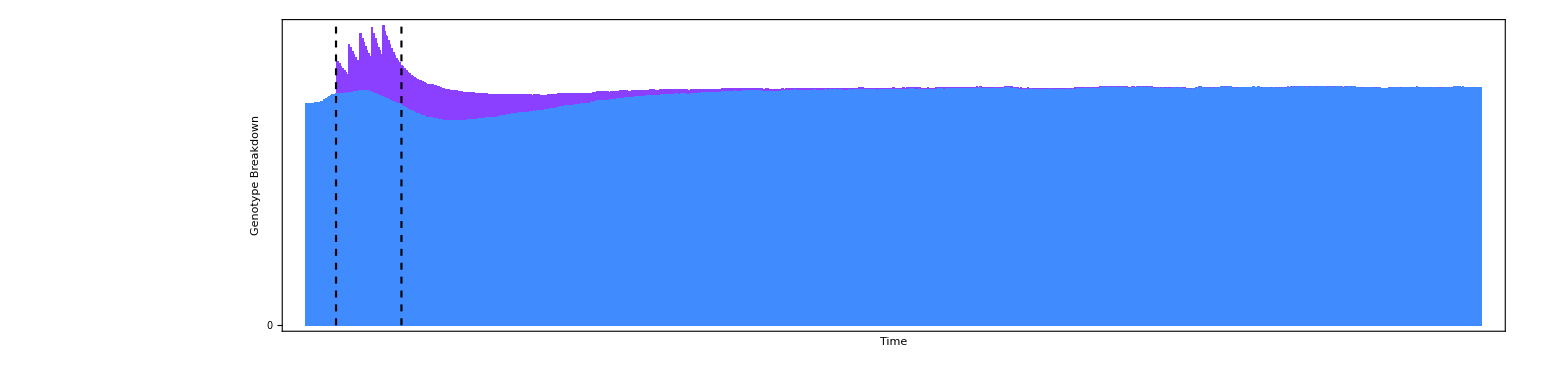

```mathematica
BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Lighter[#,.25]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{Range[0,1.5*counts//Flatten//Max,100000],None},{None,Range[0,50000,500]}}
,FrameTicksStyle->{
{Directive[Black,30],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,30]}
}
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@(releaseTimes-1))}]
]
(*Export[dataFolderName<>experimentName<>"_02.png",%,ImageSize->5000]*)
```

## 2) Factorial Grid

Setup work folder (to root where files are located)

```mathematica
USER=5;
If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/ThresholdDependent"],0];
If[USER==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/ThresholdDependent/Datasets/"],0];
If[USER==3,SetDirectory["/Users/sanchez.hmsc/Desktop/FactorialTestData/"],0];
If[USER==4,SetDirectory["/Users/sanchez.hmsc/Desktop/ThresholdDependent/"],0];
If[USER==5,SetDirectory["/Volumes/marshallShare/MGDrivE_Datasets/ThresholdDependent/Datasets/"],0];
timeRange={1,1093};
```

Load Data

Load files and setup aggregation of genotypes

```mathematica
(*:--------: User Input    :--------:*)
{experimentName,experimentFilter}={"Datasets/2018_10_04_ANALYZED","E*"};
releasesStart=20;
genotypesGroups={
{{1,1,2,2,3,3,4,5,6,1,1,2,4,4,5,7,7,8},"W"},
{{4,5,6,7,7,8,8,9,9,2,3,3,5,6,6,8,9,9},"D"}
};
(*:--------: Get Folders   :--------:*)
directoryData=Directory[]<>"/"<>experimentName<>"/";
experimentFolders=FileNames[experimentFilter,directoryData];
Length[experimentFolders]
```

0

```mathematica
factorialData=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,geography,driveSystem,releasesNumber,coverage}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
releaseTimes={releasesStart,(releasesNumber*8)+releasesStart};
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM*","AF1*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(**)
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
(*Mosquito counts*)
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
(*Mosquito Ratios*)
ratio=(#[[2]]/(#[[1]]+#[[2]])&/@{counts})[[1]];
ratioTime=Transpose[{Range[ratio//Length],ratio}];
Flatten/@({ConstantArray[{releasesNumber,coverage/1000//N},ratio//Length],ratioTime}//Transpose)
,{i,1,experimentFolders//Length}];
flattenedData=Flatten[factorialData,1];
Export["./Datasets/50UR10x.csv",flattenedData]
```

./Datasets/50UR10x.csv

```mathematica
Transpose[{
ConstantArray[2,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]
```

{{2,1.,0}}

Plot Data

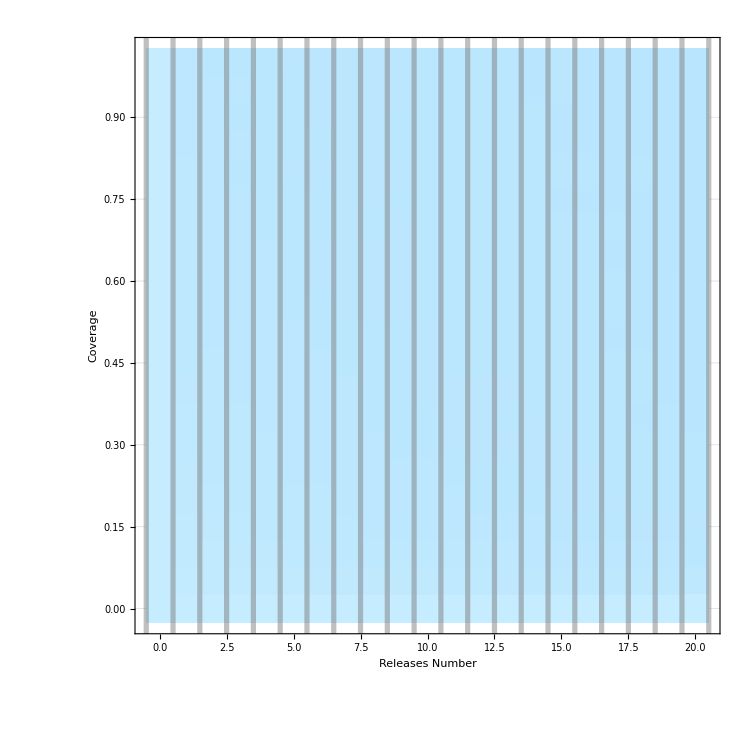

```mathematica
day=999;
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./URxy.csv"]];
contour=ListDensityPlot[
Flatten[{Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}],Transpose[{ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[1,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->750
,InterpolationOrder->0
,FrameLabel->(Style[#,50]&/@{"Releases Number","Coverage","Day: "<>StringPadLeft[ToString[day],3]})
,FrameTicksStyle->Directive[25]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
];
threeD=ListPlot3D[
Flatten[{Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}],Transpose[{ConstantArray[1,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,AxesLabel->(Style[#,30]&/@{"Releases Number","Coverage","Drive Ratio"})
,AxesStyle->Directive[25]
,BoundaryStyle->Directive[Opacity[.5],Thick]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,ImageSize->1000
,InterpolationOrder->0
,Lighting->{"Ambient",White}
,Mesh->{20,0}
,MeshStyle->Directive[Thick,Opacity[0.5]]
,PlotRange->{{-.5,20.5},{-.05,1.05},{0,1}}
,PlotRangePadding->0
,ViewPoint->{Front,Top}
];
GraphicsRow[{contour,threeD}]
```

```mathematica
barLegend=BarLegend[{"LakeColors",{0,1}}
,LabelStyle->20
,LegendLabel->Style["Drive Ratio",25]
];
```

Predictor

```mathematica
predictor=Predict[({#[[1]],#[[2]],#[[3]]}->#[[4]])&/@ flattenedData]
```

PredictorFunction[…]

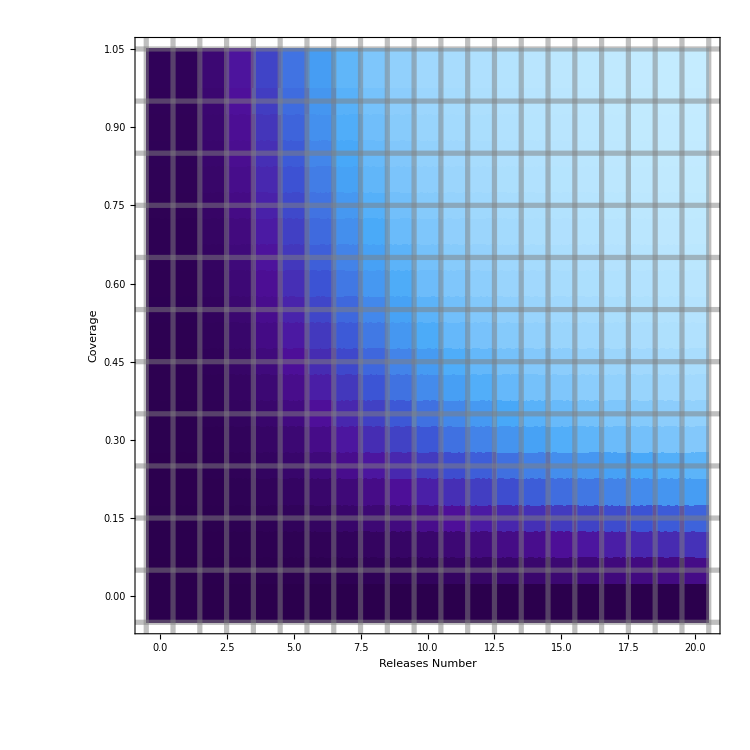

```mathematica
day=200;
probe=Table[
{x,y,predictor[{x,y,day}]}
,{x,0,20,.1}
,{y,0,1,.05}
];
contour=ListDensityPlot[
Flatten[probe,1]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->750
,InterpolationOrder->0
,FrameLabel->(Style[#,50]&/@{"Releases Number","Coverage","Day: "<>StringPadLeft[ToString[day],3]})
,FrameTicksStyle->Directive[25]
,PlotRange->{{-.5,20.5},{-.05,1.05}}
,PlotRangePadding->0
];
threeD=ListPlot3D[
Flatten[probe,1]
,AxesLabel->(Style[#,30]&/@{"Releases Number","Coverage","Drive Ratio"})
,AxesStyle->Directive[25]
,BoundaryStyle->Directive[Opacity[0.5],Thin]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ImageSize->1000
,InterpolationOrder->0
,Lighting->{"Ambient",White}
,Mesh->None
,MeshStyle->Directive[Thin,Opacity[0]]
,PlotRange->{{-.5,20.5},{-.05,1.05},{0,1}}
,PlotRangePadding->0
,ViewPoint->{Front,Top}
];
GraphicsRow[{contour,threeD}]
```

Export Video

```mathematica
contourPlots=Table[
ListDensityPlot[
Flatten[{Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}],Transpose[{ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[1,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->750
,InterpolationOrder->0
,FrameLabel->None
,FrameTicksStyle->Directive[100]
,PlotRangePadding->0
,PlotRange->{{-.5,20.5},{-.025,1.025}}
]
,{day,timeRange[[1]],timeRange[[2]]}];
threeDPlots=Table[
ListPlot3D[
Flatten[{Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}],Transpose[{ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[1,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,AxesLabel->None
,AxesStyle->Directive[75]
,BoundaryStyle->Directive[Opacity[.5],Thick]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,ImageSize->1000
,InterpolationOrder->0
,Lighting->{"Ambient",White}
,Mesh->{20,0}
,MeshStyle->Directive[Thick,Opacity[0.5]]
,PlotRange->{{-.5,20.5},{-.05,1.05},{0,1}}
,PlotRangePadding->0
,ViewPoint->{Front,Top}
]
,{day,timeRange[[1]],timeRange[[2]]}];
(*Export["contour.gif",contourPlots]*)
```

```mathematica
fileTuples=Transpose[{Range[timeRange[[1]],timeRange[[2]]],contourPlots,threeDPlots}];
Map[
Export[
"./images/"<>StringPadLeft[ToString[#[[1]]],4,"0"]<>".png",
GraphicsRow[{#[[2]],#[[3]]}],
ImageSize->3500
]&,
fileTuples
];
```

Export::noopen: Cannot open /Volumes/marshallShare/MGDrivE_Datasets/ThresholdDependent/Datasets/images/0252.png.

```mathematica
ListContourPlot3D[flattenedData
,AxesLabel->(Style[#,20]&/@{"Releases Number","Coverage","Time"})
,BoundaryStyle->Thick
,BoxRatios->{1,1,1.5}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"LakeColors",{1,.5}}]
,Contours->5
,ContourStyle->Opacity[0.75]
,ImageSize->1000
,PlotLegends->Automatic
,MeshStyle->Directive[Thin,Opacity[0]]
,ViewPoint->{Pi,Pi/2,2}(*Above*)
(*,OpacityFunction->Interval[{0.5,1}]*)
];
```

4 D Plot

```mathematica
{min,max}={.2,1};
v=Options[Plot3D,ViewPoint][[1,2]];
listDensity=ListDensityPlot3D[flattenedData
,AxesLabel->(Style[#,30]&/@{"Releases Number","Coverage","Time"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,4}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->2000
(*,PlotLegends->Automatic*)
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{2.4,1.4,1.9}(*Dynamic[v]*)
,OpacityFunction->Interval[{min,max}]
]
Export["./images/Flow_ReleasesCoverage.png",
Show[listDensity,ViewPoint->{2.4,1.4,1.9}]
]
```

-Graphics3D-

./images/Flow_ReleasesCoverage.png

Timing Data

```mathematica
flattenedData=Import[Directory[]<>"/TRSA_100.csv"];
```

## One

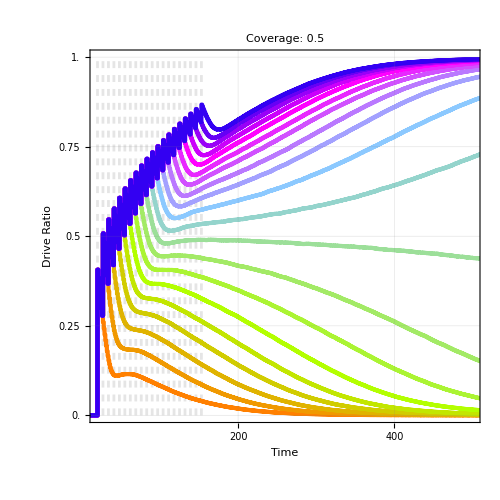

```mathematica
coverage=.5;
probed=Cases[flattenedData,{#,coverage,_,c_}->c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
plot=ListLinePlot[probed
,AspectRatio->1
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray]
,FrameTicks->{{Range[0,1,.25],None},{Flatten[{Range[0,1000,200]}],None}}
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
,PlotLabel->Style["Coverage: "<>ToString[coverage],40]
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.75,Directive[RGBColor[1, 0, 1],Opacity[1]]},{0.5,Directive[RGBColor[0.55, 0.79, 1],Opacity[1]]},{.25,Directive[RGBColor[0.7000000000000001, 1, 0.]]},{0,Directive[RGBColor[1, 0.5, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.1],Dashed,Thickness[.004],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
]
```

```mathematica
range=Range[0,1,.05];
blends=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.75,Directive[RGBColor[1, 0, 1],Opacity[1]]},{0.5,Directive[RGBColor[0.55, 0.79, 1],Opacity[1]]},{.25,Directive[RGBColor[0.7000000000000001, 1, 0.]]},{0,Directive[RGBColor[1, 0.5, 0],Opacity[1]]}},#]&/@Range[0,1,.05];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[StringPadRight[ToString[#],4,"0"],35]&/@range]
}]//Grid;
Export["colorScale.pdf",colorScale]
```

colorScale.pdf

```mathematica
colorBlender[]
```

## Batch

```mathematica
Table[
coverage=i;
probed=Cases[flattenedData,{#,coverage,_,c_}->c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
plot=ListLinePlot[probed
,AspectRatio->1
,Frame->True
,FrameLabel->(Style[#,60]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray,50]
,FrameTicks->{{Range[0,1,.25],None},{Flatten[{Range[0,1000,200]}],None}}
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
,PlotLabel->Style["Coverage: "<>ToString[coverage],75]
,PlotRange->{{(*20*10*)0,500},{0,1}}
,PlotStyle->({Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.75,Directive[RGBColor[1, 0, 1],Opacity[1]]},{0.5,Directive[RGBColor[0.55, 0.79, 1],Opacity[1]]},{.25,Directive[RGBColor[0.7000000000000001, 1, 0.]]},{0,Directive[RGBColor[1, 0.5, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.2],Dashed,Thick,Line[{{#,0},{#,1}}]&/@(Range[0,7*40-1,1*7]+20)}]
];
Export["./images/CoverageSweeps/RatioTime"<>StringPadLeft[ToString[coverage*100],4,"0"]<>"png",plot,ImageSize->2000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

{./images/CoverageSweeps/RatioTime000.png,./images/CoverageSweeps/RatioTime005.png,./images/CoverageSweeps/RatioTime010.png,./images/CoverageSweeps/RatioTime015.png,./images/CoverageSweeps/RatioTime020.png,./images/CoverageSweeps/RatioTime025.png,./images/CoverageSweeps/RatioTime030.png,./images/CoverageSweeps/RatioTime035.png,./images/CoverageSweeps/RatioTime040.png,./images/CoverageSweeps/RatioTime045.png,./images/CoverageSweeps/RatioTime050.png,./images/CoverageSweeps/RatioTime055.png,./images/CoverageSweeps/RatioTime060.png,./images/CoverageSweeps/RatioTime065.png,./images/CoverageSweeps/RatioTime070.png,./images/CoverageSweeps/RatioTime075.png,./images/CoverageSweeps/RatioTime080.png,./images/CoverageSweeps/RatioTime085.png,./images/CoverageSweeps/RatioTime090.png,./images/CoverageSweeps/RatioTime095.png,./images/CoverageSweeps/RatioTime100.png}

Predictor Timing

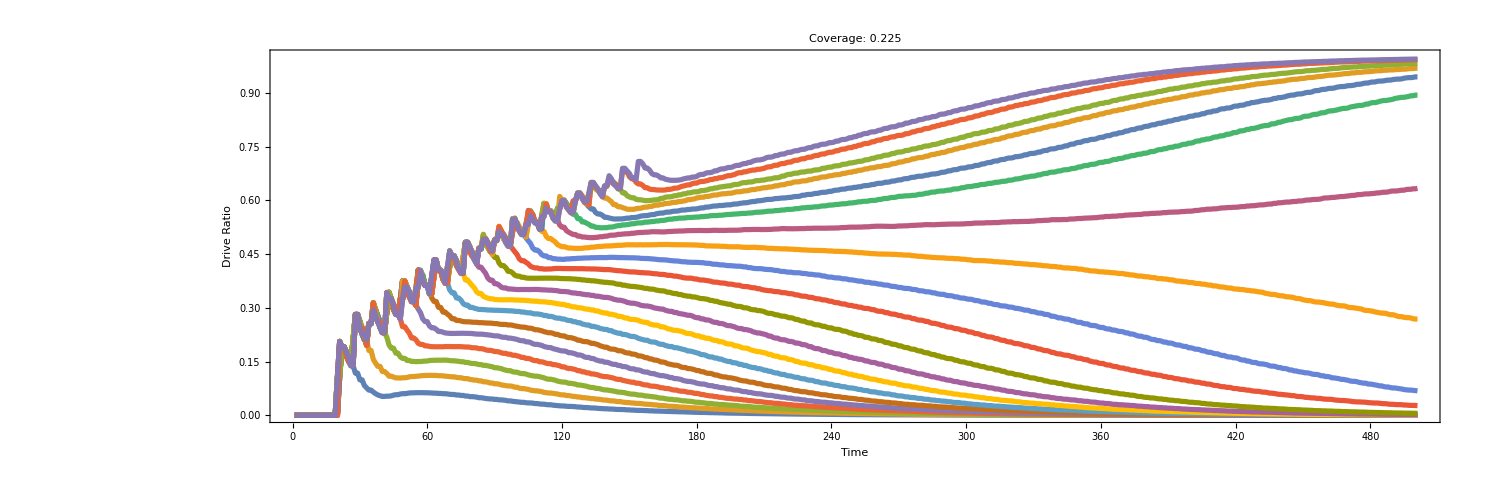

```mathematica
coverage=.225;
ListLinePlot[
Table[
predictor[{i,coverage,#}]&/@Range[0,500,1]
,{i,flattenedData[[All,1]]//DeleteDuplicates}
]
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray]
,FrameTicksStyle->20
,ImageSize->1500
,InterpolationOrder->1
,PlotLabel->Style["Coverage: "<>ToString[coverage],40]
,PlotRange->{{0,All},{0,1}}
,PlotStyle->Thickness[.0025]
]
```

## Final Plots

Response Surface (First Set)

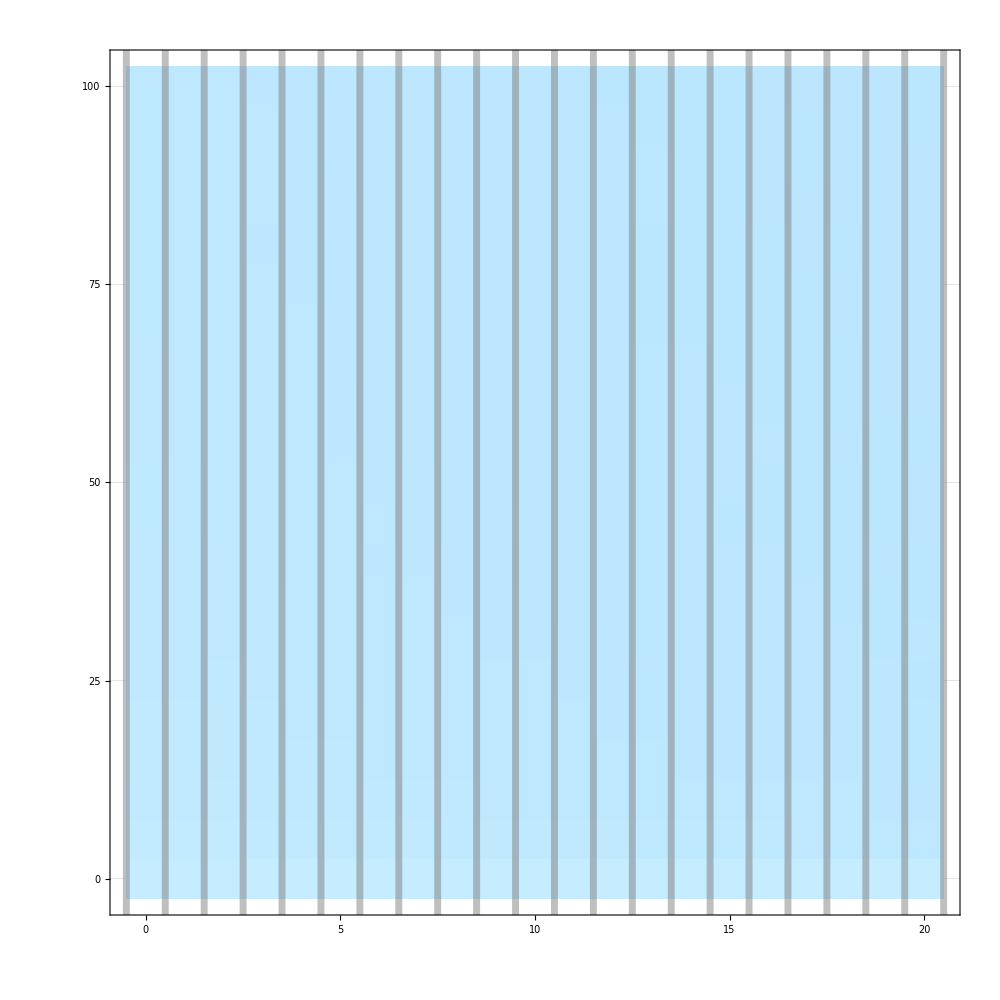

./imagesFinal/XR_URxy.pdf

```mathematica
day=1093;
experimentString="URxy";
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
{firstCol,firstRow}=ConstantArray[1,2];
filtered=If[
(StringTake[experimentString,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}]
];
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]},1]
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
]
Export["./imagesFinal/XR_"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Response Surface (Batch Migration)

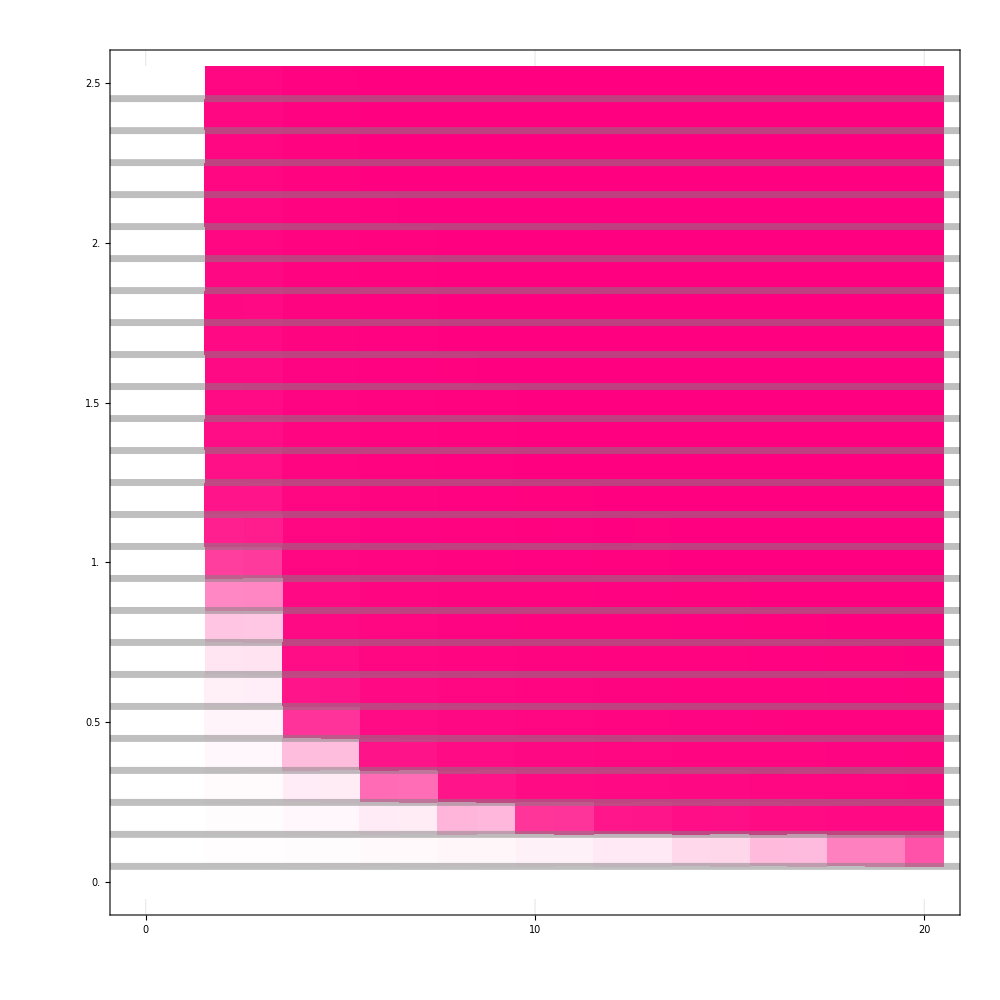

./imagesFinal/BM_UB.pdf

```mathematica
day=1093;
experimentString="UB";
multiplier=100;
flattenedData={#[[1]],#[[2]]*multiplier,Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=If[
(StringTake[experimentString,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}]
];
contour=ListDensityPlot[
Flatten[{
filtered,Transpose[{ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}],Transpose[{flattenedData[[All,1]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length],ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,41,1],Range[.05,2.5,.1]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#]}&/@Range[0,2.5,.5],None},{Range[0,40,10],None}}
,FrameTicksStyle->Directive[Bold,65]
,PlotLegends->None
,PlotRange->{{-.5,20.5},{-.05,2.55}}
,PlotRangePadding->0
]
Export["./imagesFinal/BM_"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Response Surface (Sensitivity)

## Single Experiment

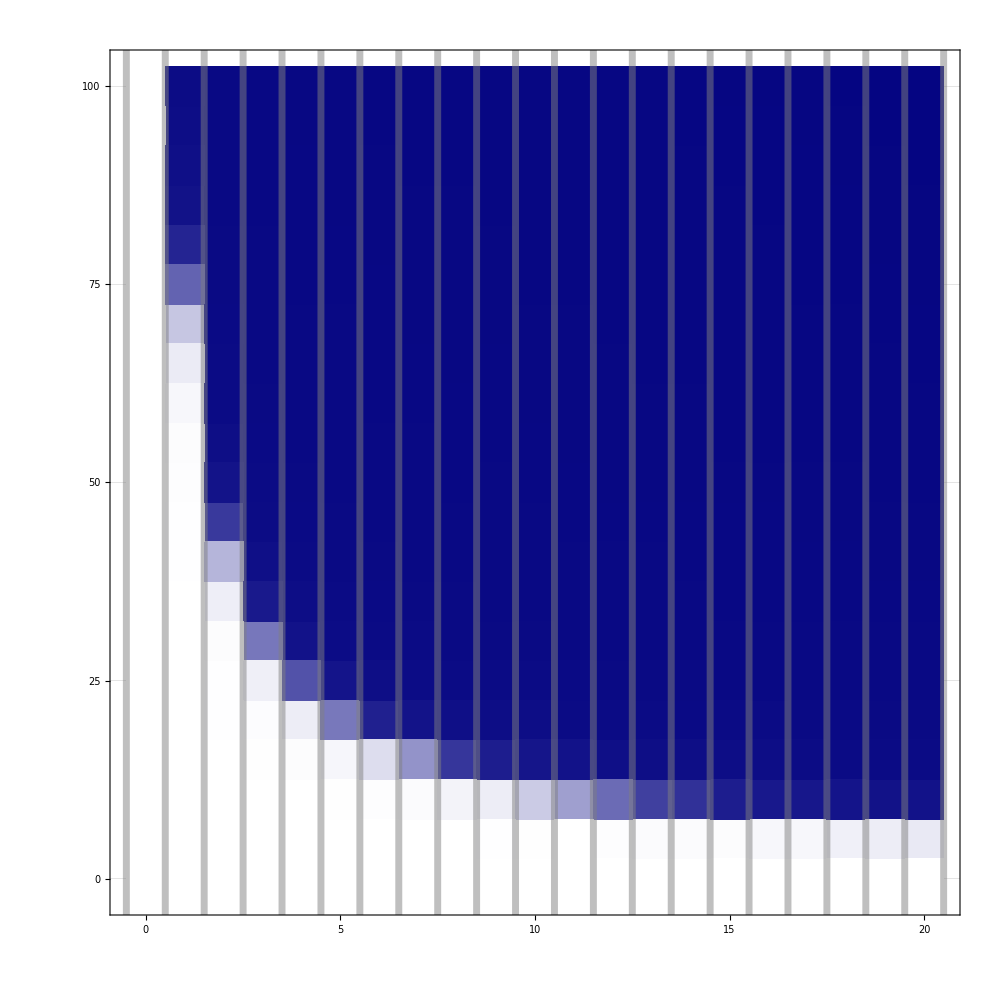

./images/UXSA_200.pdf

```mathematica
day=999;
experimentString="UXSA_200";
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}];
{firstCol,firstRow}=ConstantArray[0,2];
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#),("RSA_"<>#)}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

{{TXSA_001,TRSA_001,TXSA_002,TRSA_002,TXSA_010,TRSA_010,TXSA_020,TRSA_020,TXSA_100,TRSA_100,TXSA_200,TRSA_200},{UXSA_001,URSA_001,UXSA_002,URSA_002,UXSA_010,URSA_010,UXSA_020,URSA_020,UXSA_100,URSA_100,UXSA_200,URSA_200}}

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
(**)
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
filtered=If[i==1,filtered,{#[[1]],#[[2]],1-#[[3]]}&/@filtered];
{firstCol,firstRow}=If[(i==1)&&(StringTake[experimentString,{2}]=="R"),ConstantArray[0,2],ConstantArray[1,2]];
{firstCol,firstRow}=If[(i==2)&&(StringTake[experimentString,{2}]=="X"),ConstantArray[0,2],ConstantArray[1,2]];
(**)
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_N_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

{{./imagesFinal/SA_N_TXSA_001.pdf,./imagesFinal/SA_N_TRSA_001.pdf,./imagesFinal/SA_N_TXSA_002.pdf,./imagesFinal/SA_N_TRSA_002.pdf,./imagesFinal/SA_N_TXSA_010.pdf,./imagesFinal/SA_N_TRSA_010.pdf,./imagesFinal/SA_N_TXSA_020.pdf,./imagesFinal/SA_N_TRSA_020.pdf,./imagesFinal/SA_N_TXSA_100.pdf,./imagesFinal/SA_N_TRSA_100.pdf,./imagesFinal/SA_N_TXSA_200.pdf,./imagesFinal/SA_N_TRSA_200.pdf},{./imagesFinal/SA_N_UXSA_001.pdf,./imagesFinal/SA_N_URSA_001.pdf,./imagesFinal/SA_N_UXSA_002.pdf,./imagesFinal/SA_N_URSA_002.pdf,./imagesFinal/SA_N_UXSA_010.pdf,./imagesFinal/SA_N_URSA_010.pdf,./imagesFinal/SA_N_UXSA_020.pdf,./imagesFinal/SA_N_URSA_020.pdf,./imagesFinal/SA_N_UXSA_100.pdf,./imagesFinal/SA_N_URSA_100.pdf,./imagesFinal/SA_N_UXSA_200.pdf,./imagesFinal/SA_N_URSA_200.pdf}}

Response Surface (Sensitivity Difference)

## Single Experiment

```mathematica
experimentString="TRSA_100Diff";
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]],If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;
```

{0,-0.986649}

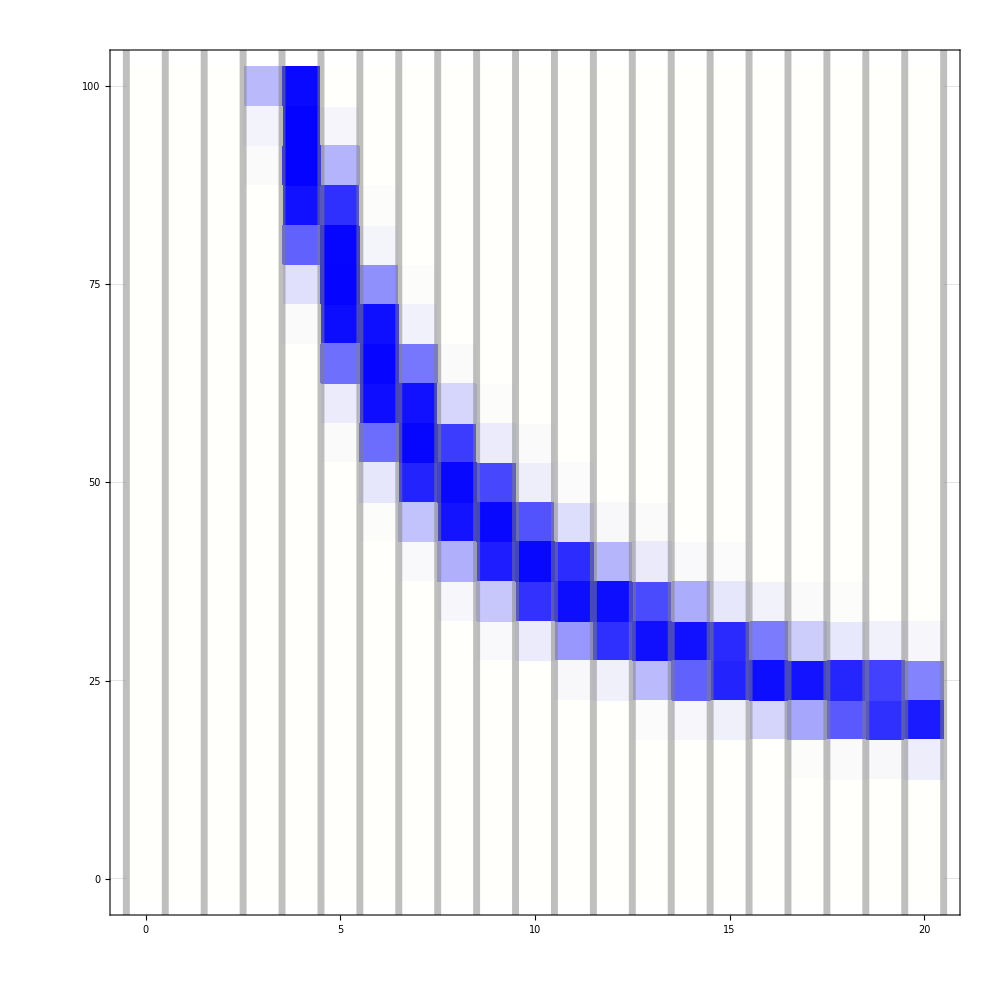

./images/TRSA_100Diff.pdf

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#<>"Diff"),("RSA_"<>#<>"Diff")}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

{{TXSA_001Diff,TRSA_001Diff,TXSA_002Diff,TRSA_002Diff,TXSA_010Diff,TRSA_010Diff,TXSA_020Diff,TRSA_020Diff,TXSA_100Diff,TRSA_100Diff,TXSA_200Diff,TRSA_200Diff},{UXSA_001Diff,URSA_001Diff,UXSA_002Diff,URSA_002Diff,UXSA_010Diff,URSA_010Diff,UXSA_020Diff,URSA_020Diff,UXSA_100Diff,URSA_100Diff,UXSA_200Diff,URSA_200Diff}}

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]],If[#[[3]]<0,#[[3]],1*(#[[3]])]}&/@flattenedData;
flattenedData=If[i==1,flattenedData,{#[[1]],#[[2]],-1*#[[3]]}&/@flattenedData];
(**)
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{-1,1}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_D_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

{{./imagesFinal/SA_D_TXSA_001Diff.pdf,./imagesFinal/SA_D_TRSA_001Diff.pdf,./imagesFinal/SA_D_TXSA_002Diff.pdf,./imagesFinal/SA_D_TRSA_002Diff.pdf,./imagesFinal/SA_D_TXSA_010Diff.pdf,./imagesFinal/SA_D_TRSA_010Diff.pdf,./imagesFinal/SA_D_TXSA_020Diff.pdf,./imagesFinal/SA_D_TRSA_020Diff.pdf,./imagesFinal/SA_D_TXSA_100Diff.pdf,./imagesFinal/SA_D_TRSA_100Diff.pdf,./imagesFinal/SA_D_TXSA_200Diff.pdf,./imagesFinal/SA_D_TRSA_200Diff.pdf},{./imagesFinal/SA_D_UXSA_001Diff.pdf,./imagesFinal/SA_D_URSA_001Diff.pdf,./imagesFinal/SA_D_UXSA_002Diff.pdf,./imagesFinal/SA_D_URSA_002Diff.pdf,./imagesFinal/SA_D_UXSA_010Diff.pdf,./imagesFinal/SA_D_URSA_010Diff.pdf,./imagesFinal/SA_D_UXSA_020Diff.pdf,./imagesFinal/SA_D_URSA_020Diff.pdf,./imagesFinal/SA_D_UXSA_100Diff.pdf,./imagesFinal/SA_D_URSA_100Diff.pdf,./imagesFinal/SA_D_UXSA_200Diff.pdf,./imagesFinal/SA_D_URSA_200Diff.pdf}}

Timing

```mathematica
experimentString=experimentString="50UX_1x_2018_09_04";
flattenedData=Import["./"<>experimentString<>".csv"];
```

```mathematica
Table[
coverage=i;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber;
plot=ListLinePlot[probed
,AspectRatio->1
,Filling->Prepend[(#->{#+1})&/@Range[1,Length[probed]-1],1->1]
,FillingStyle->Opacity[0]
,Frame->True
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None(*{{{#,StringPadRight[ToString[#],4,"0"]}&/@Range[0,1,.5],None},{Flatten[{Range[0,1000,200]}],None}}*)
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{9*20,1000},{0,1}}
,PlotStyle->({Thickness[.005],Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.2],Dashed,Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./"<>experimentString<>"_"<>StringPadLeft[ToString[coverage*100//Round],4,"0"]<>".png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

{./50UX_1x_2018_09_04_0000.png,./50UX_1x_2018_09_04_0005.png,./50UX_1x_2018_09_04_0010.png,./50UX_1x_2018_09_04_0015.png,./50UX_1x_2018_09_04_0020.png,./50UX_1x_2018_09_04_0025.png,./50UX_1x_2018_09_04_0030.png,./50UX_1x_2018_09_04_0035.png,./50UX_1x_2018_09_04_0040.png,./50UX_1x_2018_09_04_0045.png,./50UX_1x_2018_09_04_0050.png,./50UX_1x_2018_09_04_0055.png,./50UX_1x_2018_09_04_0060.png,./50UX_1x_2018_09_04_0065.png,./50UX_1x_2018_09_04_0070.png,./50UX_1x_2018_09_04_0075.png,./50UX_1x_2018_09_04_0080.png,./50UX_1x_2018_09_04_0085.png,./50UX_1x_2018_09_04_0090.png,./50UX_1x_2018_09_04_0095.png,./50UX_1x_2018_09_04_0100.png}

```mathematica
Line[{ConstantArray[0,probed[[2]]//Length],Range[1,probed[[2]]//Length],probed[[2]]}//Transpose]
```

```mathematica
Range[First[releasesNumber],Last[releasesNumber],4]
releasesNumber
```

{1.,5.,9.,13.,17.}

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.}

```mathematica
two=Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&/@Range[0,1,1]
SwatchLegend[two,{"1 release","20 releases"}]
```

{RGBColor[1, 0.5, 1, 1],RGBColor[0, 0, 1, 1]}

```mathematica
BarLegend[{Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&,{0,1}},20]
Export["swatch.pdf",%,ImageSize->1000]
```

swatch.pdf

```mathematica
(#->{#+1})&/@Range[2,10]
```

{2→{3},3→{4},4→{5},5→{6},6→{7},7→{8},8→{9},9→{10},10→{11}}

Legends

```mathematica
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleBatch.pdf",%,ImageSize->500]
BarLegend[{"DeepSeaColors",{0,1}}]
Export["./images/colorScale.pdf",%,ImageSize->500]
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleSensitivity.pdf",%,ImageSize->500]
```

./images/colorScaleBatch.pdf

./images/colorScale.pdf

./images/colorScaleSensitivity.pdf

```mathematica
SwatchLegend[
{ColorData[{"DeepSeaColors",{0,1}}][0],ColorData[{"DeepSeaColors",{0,1}}][1]},
{"0% Drive","100% Drive"}
,LegendMarkerSize->50
,LabelStyle->50
]
Export["swatchFixation.pdf",%]
```

swatchFixation.pdf